```mathematica
ΔE=π*Amp^2d*Ω;
a=π(k^2+d^2Ω^2)/(ΔE*d*Ω);
b=-k*π/(ΔE*d*Ω);
c=π/(ΔE*d*Ω);
g=-1;
Simplify[2(g*b^2-a*c*g)]
Simplify[(b^2-a*c)*(-Sqrt[(a-c)^2+4*b^2]-(a+c))]
```

2/(Amp^4 d^2 Ω^2)

(1+k^2+d^2 Ω^2+Amp^2 d^2 Ω^2 √((k^4+(-1+d^2 Ω^2)^2+2 k^2 (1+d^2 Ω^2))/(Amp^4 d^4 Ω^4)))/(Amp^6 d^4 Ω^4)

```mathematica
MajorNumerator=2/(Amp^4 d^2 Ω^2);
MajorDenominator=(1+k^2+d^2 Ω^2-Amp^2 d^2 Ω^2 √((k^4+(-1+d^2 Ω^2)^2+2 k^2 (1+d^2 Ω^2))/(Amp^4 d^4 Ω^4)))/(Amp^6 d^4 Ω^4);
MinorNumerator=2/(Amp^4 d^2 Ω^2);
MinorDenominator=(1+k^2+d^2 Ω^2+Amp^2 d^2 Ω^2 √((k^4+(-1+d^2 Ω^2)^2+2 k^2 (1+d^2 Ω^2))/(Amp^4 d^4 Ω^4)))/(Amp^6 d^4 Ω^4);

MajorAxisSq[Amp_,Ω_,d_,k_]:=Evaluate[Simplify[MajorNumerator/MajorDenominator]]
MinorAxisSq[Amp_,Ω_,d_,k_]:=Evaluate[Simplify[MajorNumerator/MinorDenominator]]
AngleOfRotation[Amp_,Ω_,d_,k_]:=Evaluate[Simplify[ArcCot[(a-c)/(2b)]/2]]
Elasticity[Ω_,d_,k_]:=√2 √((√(k^4+(-1+d^2 Ω^2)^2+2 k^2 (1+d^2 Ω^2)))/(1+k^2+d^2 Ω^2+√(k^4+(-1+d^2 Ω^2)^2+2 k^2 (1+d^2 Ω^2))))
EnergyLoss[Amp_,Ω_,d_]:=π*Amp^2*d*Ω
```

```mathematica
Manipulate[Show[ParametricPlot[{Amp*Cos[Ω*t],Amp *k *Cos[Ω*t]-Amp *d*Ω* Sin[Ω*t]},{t,0,π},PlotRange->{-1,1},PlotLabel->{{Tan[AngleOfRotation[Amp,Ω,d,k]],k,Elasticity[Ω,d,k],Sqrt[1-MinorAxisSq[Amp,Ω,d,k]/MajorAxisSq[Amp,Ω,d,k]],π*Amp^2*d*Ω}}],Graphics[{PointSize[Medium],Point[{{Cos[AngleOfRotation[Amp,Ω,d,k]]*Sqrt[-MinorAxisSq[Amp,Ω,d,k]+MajorAxisSq[Amp,Ω,d,k]],Sin[AngleOfRotation[Amp,Ω,d,k]]*Sqrt[-MinorAxisSq[Amp,Ω,d,k]+MajorAxisSq[Amp,Ω,d,k]]},{-Cos[AngleOfRotation[Amp,Ω,d,k]]*Sqrt[-MinorAxisSq[Amp,Ω,d,k]+MajorAxisSq[Amp,Ω,d,k]],-Sin[AngleOfRotation[Amp,Ω,d,k]]*Sqrt[-MinorAxisSq[Amp,Ω,d,k]+MajorAxisSq[Amp,Ω,d,k]]}}]}],ContourPlot[{(x*Cos[AngleOfRotation[Amp,Ω,d,k]]+y*Sin[AngleOfRotation[Amp,Ω,d,k]])^2/MajorAxisSq[Amp,Ω,d,k]+(x*Sin[AngleOfRotation[Amp,Ω,d,k]]-y*Cos[AngleOfRotation[Amp,Ω,d,k]])^2/MinorAxisSq[Amp,Ω,d,k]==1,y==k*x,y==x*Tan[AngleOfRotation[Amp,Ω,d,k]]},{x,-1,1},{y,-1,1},ContourStyle->{Red,Blue,Orange}]],{Amp,0.001,3},{Ω,.001,3},{d,0.001,1},{k,0.001,1}]
```

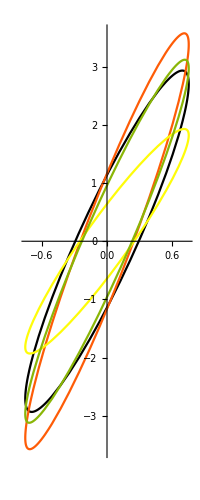
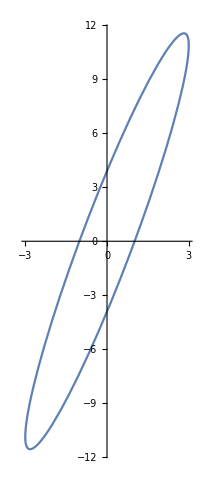

{2.68562,2.74347,1.51122,2.2607}

9.20102

```mathematica
n=4;
range=5;
xp=3;
ω=1;
InputSignal[t_]:=xp*Cos[ω*t];
For[i=1,i<n+1,i++,
Subscript[k, i]=range*RandomReal[];
Subscript[d, i]=range*RandomReal[];
Subscript[f, i][t_]:={InputSignal[t]/n,Subscript[k, i]*InputSignal[t]/n+Subscript[d, i]*InputSignal'[t]/n}]
List[ParametricPlot[Evaluate[Table[Subscript[f, i][t],{i,1,n}]],{t,0,2π},PlotStyle->ColorData[3,"ColorList"],Mesh->None,AspectRatio->Full],ParametricPlot[{InputSignal[t],Sum[Subscript[f, i][t][[2]],{i,1,n}]},{t,0,2π},AspectRatio->Full]]
Table[EnergyLoss[xp/n,ω,Subscript[d, i]],{i,1,n}]
Sum[EnergyLoss[xp/n,ω,Subscript[d, i]],{i,1,n}]
```

```mathematica
Table[ColorData[3,"ColorList"][[i]],{i,1,n}]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]}